```mathematica
2-2
```

0

NOTE: This notebook was written on, and is intended to be run on, Mathematica 6.

We will need this resource

```mathematica
P_⊗Q_:=Flatten[Table[Flatten[Table[Part[Outer[Times,P,Q],i,j,k],{j,Dimensions[P]⟦2⟧}]],{i,Dimensions[P]⟦1⟧},{k,Dimensions[Q]⟦1⟧}],1]
```

which constructs Kronecker products of matrices P and Q, whatever might be their respective dimensions. Thus

```mathematica
({{Subscript[p, 11], Subscript[p, 12]}, {Subscript[p, 21], Subscript[p, 22]}, {Subscript[p, 31], Subscript[p, 32]}})⊗({{Subscript[q, 11]}, {Subscript[q, 21]}})//MatrixForm
```

(p_11 q_11 | p_12 q_11
p_11 q_21 | p_12 q_21
p_21 q_11 | p_22 q_11
p_21 q_21 | p_22 q_21
p_31 q_11 | p_32 q_11
p_31 q_21 | p_32 q_21)

For a list of the most useful/characteristic properties of the Kronecker product, see page 24 in Chapter 1 of my Advanced Quantum Topics (2000).

# Simulation of Quantum Measurement Processes

Nicholas Wheeler
Reed College Physics Department
March 2008

### Introduction.

My objective in these exercises will be to demonstrate how Mathematica 6 can be used to create data of precisely the sort that—in the absence of instrumental difficulties—would emerge from real-world quantum mechanical experiments.

### Measurement of an observable, given that an isolated quantum system is in some prescribed state.

Two-state quantum systems—though (like all finite-dimensional systems) incapable of accommodating relations of the form

```mathematica
𝕩.𝕡-𝕡.𝕩=i ℏ 𝕀
```

—are famously well-adapted to the illustration of points of fundamental principle, which they expose in simplest-possible terms. We will make heavy use of that familiar fact. But for the purposes of this initial exercise the quantum theory of 3-state systems will better serve our needs.

To produce a random instance of a normalized complex 3-vector we proceed

```mathematica
Clear[ψ]
ψ[u_,v_,a_,b_]:=({{ⅇ^(ⅈ a)Cos[u]Cos[v]}, {ⅇ^(ⅈ b)Cos[u]Sin[v]}, {Sin[u]}})
ψ=ψ[Random[Real,{0,2π}], Random[Real,{-π/2,π/2}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
```

(-0.530286-0.13997 ⅈ
0.0887901-0.144814 ⅈ
-0.818749)

We confirm the normalization of the state

```mathematica
(Conjugate[Transpose[ψ]].ψ)⟦1⟧⟦1⟧//Chop
```

1.

and note that such a state can be prepared by filtering the output of a hermitian gun, the spectral resolution of which contains the projective term

```mathematica
𝔾=ψ.Conjugate[Transpose[ψ]]//Chop;
```

```mathematica
𝔾//MatrixForm
```

(0.300795 | -0.0268145-0.089221 ⅈ | 0.434171+0.1146 ⅈ
-0.0268145+0.089221 ⅈ | 0.0288549 | -0.0726968+0.118567 ⅈ
0.434171-0.1146 ⅈ | -0.0726968-0.118567 ⅈ | 0.67035)

I linger to demonstrate that 𝔾 is in fact a projection matrix

```mathematica
𝔾.𝔾-𝔾//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

that projects onto a 1-space

```mathematica
Eigenvalues[𝔾]//Chop
```

{1.,0,0}

which is in fact the ray defined by ψ:

```mathematica
𝔾.ψ-ψ//Chop//MatrixForm
```

(0
0
0)

Let 𝔸 be a 3×3 hermitian matrix the represents the action of an A-meter, and let us agree to work in the eigenbasis of 𝔸.
Let us (without loss of generality) agree, moreover, that the eigenvalues of 𝔸 are {-1, 0, +1}. We then have

```mathematica
𝔸=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
```

The spectral resolution of 𝔸 is 𝔸==(+1)ℙ_++(0)ℙ_0+(-1)ℙ_-with

```mathematica
SubPlus[ℙ]=({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}});
Subscript[ℙ, 0]=({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}});
SubMinus[ℙ]=({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
```

```mathematica
𝔸==(+1)SubPlus[ℙ]+(0)Subscript[ℙ, 0]+(-1)SubMinus[ℙ]
```

True

When ψ is presented to the A-meter, it

• announces ++1 with probatility prob_+, else
   • announces  0  with probatility prob_0, else
   • announces -1  with probatility prob_-

where

```mathematica
SubPlus[prob]=(Conjugate[Transpose[SubPlus[ℙ].ψ]].SubPlus[ℙ].ψ)⟦1⟧⟦1⟧//Chop
Subscript[prob, 0]=(Conjugate[Transpose[Subscript[ℙ, 0].ψ]].Subscript[ℙ, 0].ψ)⟦1⟧⟦1⟧//Chop
SubMinus[prob]=(Conjugate[Transpose[SubMinus[ℙ].ψ]].SubMinus[ℙ].ψ)⟦1⟧⟦1⟧//Chop
```

0.300795

0.0288549

0.67035

Of  course

```mathematica
SubPlus[prob]+Subscript[prob, 0]+SubMinus[prob]//Chop
```

1.

In those respective cases the A-meter creates the state

```mathematica
({{1}, {0}, {0}})else ({{0}, {1}, {0}}) else ({{0}, {0}, {1}})
```

The following construction—in which it is intended that x will be assigned a random value: 0 ⩽ x ⩽ 1 —designed to simulate the result of a solitary A-measurement:

```mathematica
MeasureA[x_]:=Which[0⩽x<SubPlus[prob], +1, SubPlus[prob]⩽x<SubPlus[prob]+Subscript[prob, 0], 0, SubPlus[prob]+Subscript[prob, 0]⩽x⩽1,-1]
```

To simulate a short series of such A-measurements, we proceed

```mathematica
TestRunA1=Table[MeasureA[Random[]],{n,1,20}]
```

{-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1}

Looking for more reliable statistics, we spend a long afternoon in the lab, and create

```mathematica
TestRunA2=Table[MeasureA[Random[]],{n,1,1000}];
```

Here is a summary of our data:

```mathematica
Count[TestRunA2,1]
Count[TestRunA2,0]
Count[TestRunA2,-1]
```

283

28

689

The average of the meter readings produced by that particular series of measurements is given by

```mathematica
MeasuredMean=(Count[TestRunA2,1]-Count[TestRunA2,-1])/1000//N
```

-0.406

What confidence should we invest in our "averaged meter reading"? To answer that question, one should—according to John R. Taylor, An Introduction to Error Analysis (1982) §4.4 and

```mathematica
Hyperlink["Standard deviation of the mean","http://www.statsdirect.com/help/basic_descriptive_statistics/standard_deviation.htm"]
```

—look to the construction

```mathematica
SDM=(√((∑_(k=1)^1000 (TestRunA2⟦k⟧-MeasuredMean)^2)/(1000-1)))/(√1000)
```

0.0284248

The following construction provides graphic indication of how our measured mean compares with the theoretically predicted mean

```mathematica
PredictedMean=(Conjugate[Transpose[ψ]].𝔸.ψ)⟦1⟧⟦1⟧//Chop
```

-0.369555

and of how much confidence we can invest in the experimental result:

```mathematica
MakeFigure[m_,σ_,α_]:=Plot[1/(σ √(2π))Exp[-1/2((x-m)/σ)^2],{x,-(1+2σ),(1+2σ)}, GridLines->{{m,{α,Red}},{}}, PlotRange->{0,3/(2σ √(2π))}, Ticks->{{-1,α, 1},{}},
PlotLabel->Style["Comparison of measured and predicted means",  FontFamily->"Helvetica", FontSize->14]]
```

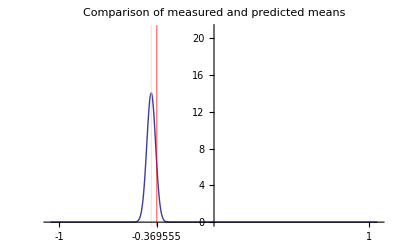

```mathematica
MakeFigure[MeasuredMean,SDM, PredictedMean]
```

Finally, I place all state-construction commands and all state-dependent commands within a single cell, so that a fresh series of N   measurements (I have set N = 1000, but the value of N is very easily adjusted) can be simulated at a single keystroke:

(0.428699-0.599788 ⅈ
-0.594421+0.29904 ⅈ
-0.117087)

0.543529

0.442762

0.0137093

539

449

12

0.527

0.529819

0.0409797

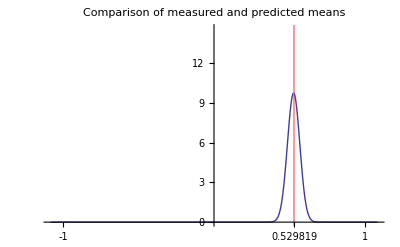

```mathematica
Clear[ψ]
ψ[u_,v_,a_,b_]:=({{ⅇ^(ⅈ a)Cos[u]Cos[v]}, {ⅇ^(ⅈ b)Cos[u]Sin[v]}, {Sin[u]}})
ψ=ψ[Random[Real,{0,2π}], Random[Real,{-π/2,π/2}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
SubPlus[prob]=(Conjugate[Transpose[SubPlus[ℙ].ψ]].SubPlus[ℙ].ψ)⟦1⟧⟦1⟧//Chop
Subscript[prob, 0]=(Conjugate[Transpose[Subscript[ℙ, 0].ψ]].Subscript[ℙ, 0].ψ)⟦1⟧⟦1⟧//Chop
SubMinus[prob]=(Conjugate[Transpose[SubMinus[ℙ].ψ]].SubMinus[ℙ].ψ)⟦1⟧⟦1⟧//Chop
NewRun=Table[MeasureA[Random[]],{n,1,1000}];
Count[NewRun,1]
Count[NewRun,0]
Count[NewRun,-1]
MeasuredMean=(Count[NewRun,1]-Count[NewRun,-1])/1000//N
PredictedMean=(Conjugate[Transpose[ψ]].𝔸.ψ)⟦1⟧⟦1⟧//Chop
SDM=(√((∑_(k=1)^1000 (TestRunA2⟦k⟧-MeasuredMean)^2)/(1000-1)))/(√1000)
MakeFigure[MeasuredMean,SDM, PredictedMean]
```

It is instructive to execute the preceding command repeatedly.

### Bohm's realization of the EPR experiment.

The original EPR paper ("Can quantum-mechanical description of reality be considered complete?", Phys. Rev. 47, 777-780 (1935)) ran to not quite four pages, contained only 18 numbered equations, and spoke only in the broadest of terms about quantum mechanical particulars. Bohr's prompt "refutation" (same title, Phys. Rev. 48, 696-702 (1935)) contained no numbered equations, and adopted a language even farther removed from computational/observational particulars. The subject was first brought into sharp focus by David Bohm, in §§ 15-19, Chapter 22 of his Quantum Theory (1951). It was Bohm who asked what might be the experience of Alice and Bob if they were to examine the widely separated components of a composite system assembled from a pair of spin one-half particles. I look here to the simulated particulars of the simplest of what have by now become a rich assortment of "Alice & Bob experiments."

Imagine it to be the case that two 2-state systems, though now widely separated (one is in Alice's lab, the other in Bob's—far away), were born and remain components of a single composite system, the quantum state of which can be described as a Kronecker product

```mathematica
({{Subscript[α, 1]}, {Subscript[α, 2]}})⊗({{Subscript[β, 1]}, {Subscript[β, 2]}})//MatrixForm
```

(α_1 β_1
α_1 β_2
α_2 β_1
α_2 β_2)

in disentangled cases, but must in the general case be considered to be entangled, i.e., to have the form (ψ_1
ψ_2
ψ_3
ψ_4)but to resist Kronecker-factorization.

Construction of a random 4-component state vector:

```mathematica
Clear[ψ,u,v,w,a,b,c]
```

To construct a random instance of a complex 4-vector of unit length we can (if we agree to discard a quantum mechanically irrelevant over-all phase factor ⅇ^(ⅈ α)) proceed

```mathematica
Clear[ψ]
ψ[u_,v_,w_,a_,b_,c_]:=({{ⅇ^(ⅈ a)Cos[u]Cos[v]Cos[w]}, {ⅇ^(ⅈ b)Cos[u]Cos[v]Sin[w]}, {ⅇ^(ⅈ c)Cos[u]Sin[v]}, {Sin[u]}})
ψ=ψ[Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
```

(-0.0190366+0.0320861 ⅈ
-0.0553404-0.0419384 ⅈ
-0.0291799+0.0233005 ⅈ
-0.996189)

We verify that the state just described does indeed have unit norm:

```mathematica
(Conjugate[Transpose[ψ]].ψ)⟦1⟧⟦1⟧//Chop
```

1.

Representation of Alice/Bob's measurement devices:

In 2-state theory, all measurement devices ("meters") can be represented by traceless 2×2 hermitian matrices. All such matrices can be developed  𝕄=m_1 σ_1+m_2 σ_2+m_3 σ_3, where

```mathematica
𝕀=({{1, 0}, {0, 1}});
Subscript[σ, 1]=({{0, 1}, {1, 0}});
Subscript[σ, 2]=({{0, -ⅈ}, {ⅈ, 0}});
Subscript[σ, 3]=({{1, 0}, {0, -1}});
```

and (m_1
m_2
m_3) is a real 3-vector, and can without loss of generality be assumed to be a unit vector.

```mathematica
𝕄=Subscript[m, 1] Subscript[σ, 1]+Subscript[m, 2] Subscript[σ, 2]+Subscript[m, 3] Subscript[σ, 3];
𝕄//MatrixForm
```

(m_3 | m_1-ⅈ m_2
m_1+ⅈ m_2 | -m_3)

The spectra of all such matrices are identical:

```mathematica
Eigenvalues[𝕄]/.Subscript[m, 1]^2+Subscript[m, 2]^2+Subscript[m, 3]^2->1
```

{-1,1}

We will, for the purposes of the present discussion, assume that Alice and Bob are equipped with identical meters, identified by the vector  (0
0
1):

Which is to say: both, when studying isolated/non-composite systems, use meters with the same matrix representation:

```mathematica
𝕞=({{1, 0}, {0, -1}});
```

But when Alice and Bob work as confederates in the study of composite pairs of 2-state systems the matrix representations of their respective  meters have to be adjusted, and become distinct:

```mathematica
𝔸=𝕞⊗𝕀;
𝔹=𝕀⊗𝕞;
```

From

```mathematica
𝔸//MatrixForm
𝔹//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

the spectra of Alice/Bob's meters become obvious: their meters continue to read ±1, just as they did when used to study isolated 2-state systems. Also obvious are the following spectral resolutions 𝔸=ℙA_+-ℙA_-, 𝔹=ℙB_+-ℙB_- where the ℙ-matrices project onto 2-dimensional subspaces of 4-space:

```mathematica
SubPlus[PA]=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
SubMinus[PA]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
SubPlus[PB]=({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}})
SubMinus[PB]=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})
```

{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

{{1,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}

{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,1}}

Experimental protocol:

The experimental set-up to be employed by Alice and Bob is diagrammed below:

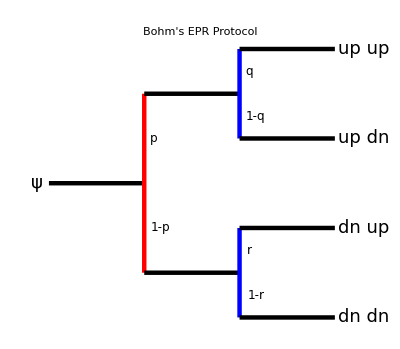

```mathematica
Show[Graphics[{Thickness[0.008],Line[{{0,0},{1,0}}]}],
Graphics[{Red,Thickness[0.008],Line[{{1,-1},{1,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,+1},{2,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,-1},{2,-1}}]}],
Graphics[{Blue,Thickness[0.008],Line[{{2,1/2},{2,3/2}}]}],
Graphics[{Blue,Thickness[0.008],Line[{{2,-1/2},{2,-3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,3/2},{3,3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,1/2},{3,1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-1/2},{3,-1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-3/2},{3,-3/2}}]}],
Graphics[Text[Style["p", FontSize->12],{1.1,0.5}]],
Graphics[Text[Style["1-p", FontSize->12],{1.17,-0.5}]],
Graphics[Text[Style["q", FontSize->12],{2.1,1.25}]],
Graphics[Text[Style["1-q", FontSize->12],{2.17,.75}]],
Graphics[Text[Style["r", FontSize->12],{2.1,-.75}]],
Graphics[Text[Style["1-r", FontSize->12],{2.17,-1.25}]],Graphics[Text[Style["up up", FontSize->18],{3.3,1.50}]],
Graphics[Text[Style["up dn", FontSize->18],{3.3,0.50}]],
Graphics[Text[Style["dn up", FontSize->18],{3.3,-0.50}]],
Graphics[Text[Style["dn dn", FontSize->18],{3.3,-1.50}]],
Graphics[Text[Style["ψ", FontSize->18],{-0.13,0}]],
PlotLabel->Style["Bohm's EPR Protocol", Blue, FontFamily->"Helvetica", FontSize->14]]
```

REMARK: I will consider the {up, dn} and {+1, -1} notations to be equivalent.

STAGE #1: The state ψ is presented to Alice. Her meter reads up with probability

```mathematica
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
```

0.00621329

and creates (which Alice ships on to Bob) the (normalized) state

```mathematica
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop;
```

Else (with probability 1 - p) it reads dn, signifying that Alice's meter has created/shipped the state

```mathematica
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop;
```

```mathematica
Au//MatrixForm
Ad//MatrixForm
```

(-0.241506+0.407058 ⅈ
-0.702071-0.532048 ⅈ
0
0)

(0
0
-0.029271+0.0233732 ⅈ
-0.999298)

STAGE #2: If Bob receives Au then his meter reads up with probability

```mathematica
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop;
```

else (with probability 1 - q) it reads dn. If, on the other hand, Bob receives Ad then his meter reads up with probability

```mathematica
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop;
```

```mathematica
q
r
```

0.224021

0.0014031

else (with probability 1 - r) it reads dn. We have no interest in the states prepared/exported by Bob's meter.

From the figure we are led to the following doubly contingent construction, where 0 ⩽ x, y, z ⩽ 1 are understood to be independent random numbers.

```mathematica
Which[0⩽x<p,Which[0⩽y<q,{up,up},q⩽y⩽1,{up,dn}],p⩽x⩽1,Which[0⩽z<r,{dn,up},r⩽z⩽1,{dn,up}]]
```

The values assumed by the probabilities p, q, r are contingent only upon the value assigned to the state ψ that has been presented to Alice.

```mathematica
AliceBobProtocol[x_,y_,z_]:=Which[0⩽x<p,Which[0⩽y<q,upup,q⩽y⩽1,updn],p⩽x⩽1,Which[0⩽z<r,dnup,r⩽z⩽1,dndn]]
```

The following table records the results obtained from 1000 repetitions of the experiment:

```mathematica
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[],ψ],{n,1,1000}]
```

{dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,upup,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,updn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn,dndn}

Statistical analysis of such data

We assemble the raw data

```mathematica
Count[AliceBobResults,upup]
Count[AliceBobResults,updn]
Count[AliceBobResults,dnup]
Count[AliceBobResults,dndn]
```

15

11

0

974

and, to check the accuracy of the numbers, compute

```mathematica
Count[AliceBobResults,upup]+Count[AliceBobResults,updn]+Count[AliceBobResults,dnup]+Count[AliceBobResults,dndn]
```

1000

Interpreting frequency of occurance to provide an estimate of the probability of occurance, we construct

```mathematica
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
```

0.015

0.011

0.

0.974

```mathematica
Subscript[P, upup]+Subscript[P, updn]+Subscript[P, dnup]+Subscript[P, dndn]
```

1.

We have interest in the degree to which Alice's/Bob's meter readings are correlated.  If x and y are (possibly interdependent) random variables, then Pearson's correlation coefficient

```mathematica
Hyperlink["Correlation Coefficient","http://www.vias.org/tmdatanaleng/cc_corr_coeff.html"]
```

is defined

```mathematica
(average of product-product of averages)/(√((⟨x^2⟩-⟨x⟩^2)(⟨y^2⟩-⟨y⟩^2)))
```

In the present context, we interpret updn to mean (+1)(-1), etc., and so arrive at the construction

```mathematica
CorrelationCoefficient[x_,y_,z_,w_]:=(((x+w)-(y+z))-((x+y)-(z+w))((x+z)-(y+w)))/(√((1-((x+y)-(z+w))^2)(1-((x+z)-(y+w))^2)))
```

```mathematica
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

0.755301

Here I again conflate all relevant constructions/commands, so as to make it possible to simulate a run of 1000 Alice/Bob experiments with a single keystroke:

```mathematica
Clear[ψ,p,q,r, Au, Ad]
ψ[u_,v_,w_,a_,b_,c_]:=({{ⅇ^(ⅈ a)Cos[u]Cos[v]Cos[w]}, {ⅇ^(ⅈ b)Cos[u]Cos[v]Sin[w]}, {ⅇ^(ⅈ c)Cos[u]Sin[v]}, {Sin[u]}})
ψ=ψ[Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

(-0.308001+0.648793 ⅈ
-0.168157-0.509343 ⅈ
-0.290013+0.272867 ⅈ
0.194761)

0.803504

{{-0.343604+0.723789 ⅈ},{-0.187595-0.56822 ⅈ},{0},{0}}

{{0},{0},{-0.654246+0.615566 ⅈ},{0.439364}}

0.641934

0.806959

0.513

0.282

0.171

0.034

-0.163997

Special case: input state fully disentangled

The following command constructs at random a fully disentangled composite state and confirms its normalization:

```mathematica
disentangled[u_,a_,v_,b_]:=({{ⅇ^(ⅈ a)Cos[u]}, {Sin[u]}})⊗({{ⅇ^(ⅈ b)Cos[v]}, {Sin[v]}})
ψ=disentangled[Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
(Conjugate[Transpose[%]].%)⟦1⟧⟦1⟧//Chop
```

(-0.594262+0.244071 ⅈ
0.364405+0.473011 ⅈ
0.0927381-0.339416 ⅈ
-0.32703)

1.

The following command simulates the Alice/Bob data that would be generated if such a disentangled state were admitted as input:

```mathematica
Clear[ψ,p,q,r, Au, Ad]
disentangled[u_,a_,v_,b_]:=({{ⅇ^(ⅈ a)Cos[u]}, {Sin[u]}})⊗({{ⅇ^(ⅈ b)Cos[v]}, {Sin[v]}})
ψ=disentangled[Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}],Random[Real,{0,2π}]];
ψ//MatrixForm
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

(0.0218883+0.291145 ⅈ
0.394832-0.0597686 ⅈ
0.0385354-0.511489 ⅈ
-0.701559)

0.244709

{{0.0442474+0.588551 ⅈ},{0.798155-0.120823 ⅈ},{0},{0}}

{{0},{0},{0.0443408-0.588544 ⅈ},{-0.807248}}

0.34835

0.34835

0.088

0.16

0.253

0.499

0.0167646

It will be noticed the correlation coefficient turns out, on each repetition, to be quite small (typically of the order 0.01). The implication—as sharp as a finite data set can make it—is that Alice's and Bob's meter readings become statistically independent when the input state ψ is disentangled.

Special case: input state maximally entangled—"spooky action at a distance"

Bohm supposed our reference to "2-state systems" to be a reference specifically to particles with spin 1/2. The quantum theory of such particles is embedded in the larger quantum theory of angular momentum, in which, for natural reasons, the "singlet state"  (↑↓-↓↑)/(√2) plays a prominent role. From

```mathematica
UP=({{1}, {0}});
DN=({{0}, {1}});
```

one constructs the so-called "Bell states"

```mathematica
Bell1=(UP⊗UP+DN⊗DN)/(√2)
Bell2=(UP⊗UP-DN⊗DN)/(√2)
Bell3=(UP⊗DN+DN⊗UP)/(√2)
Bell4=(UP⊗DN-DN⊗UP)/(√2)
```

{{1/(√2)},{0},{0},{1/(√2)}}

{{1/(√2)},{0},{0},{-1/(√2)}}

{{0},{1/(√2)},{1/(√2)},{0}}

{{0},{1/(√2)},{-1/(√2)},{0}}

which are distinguished for reasons having nothing specifically to do with angular momentum, but by the fact that they are (in a sense that I will not attempt here to make precise) "maximally entangled." Evidently "4th Bell state" and  "singlet state"  refer to the same 4-dimensional object.

Suppose the state presented to Alice is the 1st Bell state. We then have

```mathematica
Clear[ψ,p,q,r, Au, Ad]
ψ=Bell1
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

{{1/(√2)},{0},{0},{1/(√2)}}

1/2

{{1},{0},{0},{0}}

{{0},{0},{0},{1}}

1

0

0.465

0.

0.

0.535

1.

We see that updn and dnup  meter readings never appear. Though Bob's lab was arbitrarily distant from Alice's, when they compare data at the end of the day they find that their data is perfectly correlated: Alice's meter read up and dn with roughly equal frequency, but each time her meter read up (else dn), do did Bob's. Presentation of Bell2 to Alice leads to a similar situation:

```mathematica
Clear[ψ,p,q,r, Au, Ad]
ψ=Bell2
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

{{1/(√2)},{0},{0},{-1/(√2)}}

1/2

{{1},{0},{0},{0}}

{{0},{0},{0},{-1}}

1

0

0.49

0.

0.

0.51

1.

while Bell3 and Bell4 lead to perfectly anticorrelated data sets:

```mathematica
Clear[ψ,p,q,r, Au, Ad]
ψ=Bell3
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

{{0},{1/(√2)},{1/(√2)},{0}}

1/2

{{0},{1},{0},{0}}

{{0},{0},{1},{0}}

0

1

0.

0.464

0.536

0.

-1.

```mathematica
Clear[ψ,p,q,r, Au, Ad]
ψ=Bell4
p=(Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧//Chop
Au=(SubPlus[PA].ψ)/(√((Conjugate[Transpose[SubPlus[PA].ψ]].SubPlus[PA].ψ)⟦1⟧⟦1⟧))//Chop
Ad=(SubMinus[PA].ψ)/(√((Conjugate[Transpose[SubMinus[PA].ψ]].SubMinus[PA].ψ)⟦1⟧⟦1⟧))//Chop
q=(Conjugate[Transpose[SubPlus[PB].Au]].SubPlus[PB].Au)⟦1⟧⟦1⟧//Chop
r=(Conjugate[Transpose[SubPlus[PB].Ad]].SubPlus[PB].Ad)⟦1⟧⟦1⟧//Chop
AliceBobResults=Table[AliceBobProtocol[Random[],Random[],Random[]],{n,1,1000}];
Subscript[P, upup]=Count[AliceBobResults,upup]/1000//N
Subscript[P, updn]=Count[AliceBobResults,updn]/1000//N
Subscript[P, dnup]=Count[AliceBobResults,dnup]/1000//N
Subscript[P, dndn]=Count[AliceBobResults,dndn]/1000//N
CorrelationCoefficient[Subscript[P, upup],Subscript[P, updn],Subscript[P, dnup],Subscript[P, dndn]]
```

{{0},{1/(√2)},{-1/(√2)},{0}}

1/2

{{0},{1},{0},{0}}

{{0},{0},{-1},{0}}

0

1

0.

0.46

0.54

0.

-1.

It is striking that the (anti)correlation is perfect: it is not that the "forbidden" data sets seldom occur, they never occur.

EPR, dismissing "spooky action at a distance" as  physical impossibility, argued that up/dn instructions had to have been written into the particles at the moment of their inception, by means of "hidden variables" of which orthodox quantum mechanics took no account. They concluded that orthodox quantum mechanics was an incomplete physical theory. EPR appeared in 1935, but de Broglie had come on different grounds to a similar conclusion already in the late 1920s. Which may account for the fact that already in his Mathematical Foundations of Quantum Mechanics (1932) von Neumann had supplied a "proof" that no deterministic hidden variable theory could account for the essential elements of quantum statistics.

### Simulated quantum violation of Bell's inequality.

It was apparently John Bell who first noticed and drew attention to the fact that von Neumann's "proof"—though it had for thirty years been universally accorded a central place in quantum mythology—contained a fatal flaw. He himself initiated the line of theoretical/experimental activity that is responsible for the present almost universally shared conviction that hidden-variable theories cannot succeed, that quantum mechanics is as strange as—even strange than—it seems. Which is ironic, for he himself was intuitively predisposed to favor hidden variable theories, and insisted until the end of his life that a sufficiently refined hidden variable theory might well lie in the future of quantum mechanics.

Bell adopted Bohm's Alice/Bob set-up, but with this difference: Alice was equipped with two meters (𝕒 and 𝕔), and so was Bob (𝕓 and 𝕔). And Bohm's assumption that 𝕒 = 𝕓 was abandoned. The meters—represented by 2×2 hermitian matrices—have σ-coordinates

```mathematica
a=({{Subscript[a, 1]}, {Subscript[a, 2]}, {Subscript[a, 3]}}), b=({{Subscript[b, 1]}, {Subscript[b, 2]}, {Subscript[b, 3]}}), c=({{Subscript[c, 1]}, {Subscript[c, 2]}, {Subscript[c, 3]}})   :   real unit vectors
```

Bell demonstrated that if Alice and Bob use there a and b meters, and if  P[a, b]  denotes the averaged product of their meter readings (at this point it becomes most natural to assume that there meters read not "up/dn" but ±1), then all hidden variable theories lead, under certain very weak hypotheses, to the expectation that

```mathematica
Abs[P[a,b]-P[a,c]]-P[b,c]⩽1
```

which is Bell's inequality. Bell also remarks without explicit demonstration (for the detailed argument see pages 66-68 in Chapter 2 of my Advanced Quantum Topics (2000) that if the state presented to Alice is the singlet state

```mathematica
Subscript[Ψ, singlet]=1/(√2)({{0}, {1}, {-1}, {0}})
```

{{0},{1/(√2)},{-1/(√2)},{0}}

then orthodox quantum mechanics supplies this simple description of the expected value of the average product:

```mathematica
P[a,b]=-a.b
```

If quantum mechanics were consistent with the hidden variable hypothesis then one would expect to have

```mathematica
Abs[a.(b-c)]+b.c⩽1
```

But it is possible to find unit 3-vectors that violate this inequality. For suppose the vectors lie all in the same plane: writing

```mathematica
β=a ∠ b
γ=a ∠ c
```

one has

```mathematica
γ-β=b ∠ c
```

The expression on the left side of the equality has become

```mathematica
Bell[β_,γ_]:=Abs[Cos[β]-Cos[γ]]+Cos[γ-β]
```

which when plotted

```mathematica
Plot3D[Bell[β,γ],{β,0,2π},{γ,0,2π}, Ticks->{{0,π/2,π,3π/2,2π},{0,π/2,π,3π/2,2π},{0,1}}]
```

-Graphics3D-

shows clearly that there are points on the (β, γ)-plane where the Bell inequality is violated. The violation appears to be maximal in the neighborhood of (β, γ) = (π/4, 3π/4), where we have

```mathematica
Bell[π/4,3π/4]
```

√2

Let us therefore set

```mathematica
a=({{0}, {0}, {1}})
b=({{0}, {Sin[π/4]}, {Cos[π/4]}})
c=({{0}, {Sin[3π/4]}, {Cos[3π/4]}})
```

{{0},{0},{1}}

{{0},{1/(√2)},{1/(√2)}}

{{0},{1/(√2)},{-1/(√2)}}

which give

```mathematica
𝕒=Subscript[σ, 3];
𝕓=1/(√2)Subscript[σ, 2]+1/(√2)Subscript[σ, 3];
𝕔=1/(√2)Subscript[σ, 2]-1/(√2)Subscript[σ, 3];
```

```mathematica
𝕒//MatrixForm
𝕓//MatrixForm
𝕔//MatrixForm
```

(1 | 0
0 | -1)

(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | -1/(√2))

(-1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

So that they can undertake collaborative work, we equip Alice with an A-meter and a C-meter

```mathematica
𝔸=𝕒⊗𝕀;
ℂ𝔸=𝕔⊗𝕀;
```

```mathematica
𝔸//MatrixForm
ℂ𝔸//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(-1/(√2) | 0 | -ⅈ/(√2) | 0
0 | -1/(√2) | 0 | -ⅈ/(√2)
ⅈ/(√2) | 0 | 1/(√2) | 0
0 | ⅈ/(√2) | 0 | 1/(√2))

and we equip Bob with a B-meter and his own kind of C-meter

```mathematica
𝔹=𝕀⊗𝕓;
ℂ𝔹=𝕀⊗𝕔;
```

```mathematica
𝔹//MatrixForm
ℂ𝔹//MatrixForm
```

(1/(√2) | -ⅈ/(√2) | 0 | 0
ⅈ/(√2) | -1/(√2) | 0 | 0
0 | 0 | 1/(√2) | -ⅈ/(√2)
0 | 0 | ⅈ/(√2) | -1/(√2))

(-1/(√2) | -ⅈ/(√2) | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0
0 | 0 | -1/(√2) | -ⅈ/(√2)
0 | 0 | ⅈ/(√2) | 1/(√2))

Those four 4×4 matrices have identical spectra:

```mathematica
Eigenvalues[𝔸]
Eigenvalues[𝔹]
Eigenvalues[ℂ𝔸]
Eigenvalues[ℂ𝔹]
```

{-1,-1,1,1}

{-1,-1,1,1}

{-1,-1,1,1}

«1 more identical outputs»

We stand in need of their spectral resolutions; i.e., we need to be in position to write

𝔸 = 𝔸up - 𝔸dn
𝔹 = 𝔹up - 𝔹dn
ℂ𝔸 = ℂ𝔸up - ℂ𝔸dn
ℂ𝔹 = ℂ𝔹up - ℂ𝔹dn

where the matrices on the right comprise four sets of complete orthogonal projection matrices.

For the A-matrix this work has already been accomplished; we have

```mathematica
𝔸up=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
𝔸dn=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
𝔸==𝔸up-𝔸dn
```

{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

True

Turning now to the B-matrix, we use

```mathematica
Eigensystem[𝔹]
```

{{-1,-1,1,1},{{0,0,-(ⅈ (-2+√2))/(√2),1},{-(ⅈ (-2+√2))/(√2),1,0,0},{0,0,-(ⅈ (2+√2))/(√2),1},{-(ⅈ (2+√2))/(√2),1,0,0}}}

to construct orthonormal eigenvectors (presented here as complex column vectors):

```mathematica
Bdn1=Transpose[{{0,0,-(ⅈ (-2+√2))/(√2),1}}]/(√(4-2 √2));
Bdn2=Transpose[{{-(ⅈ (-2+√2))/(√2),1,0,0}}]/(√(4-2 √2));
Bup1=Transpose[{{0,0,-(ⅈ (2+√2))/(√2),1}}]/(√(4+2 √2));
Bup2=Transpose[{{-(ⅈ (2+√2))/(√2),1,0,0}}]/(√(4+2 √2));
```

I demonstrate that the vectors are normalized

```mathematica
(Conjugate[Transpose[Bdn1]].Bdn1)⟦1⟧⟦1⟧//Simplify
(Conjugate[Transpose[Bdn2]].Bdn2)⟦1⟧⟦1⟧//Simplify
(Conjugate[Transpose[Bup1]].Bup1)⟦1⟧⟦1⟧//Simplify
(Conjugate[Transpose[Bup2]].Bup2)⟦1⟧⟦1⟧//Simplify
```

1

1

1

«1 more identical outputs»

and that within the up/down subspaces they are orthogonal:

```mathematica
(Conjugate[Transpose[Bup1]].Bup2)⟦1⟧⟦1⟧//Simplify
(Conjugate[Transpose[Bdn1]].Bdn2)⟦1⟧⟦1⟧//Simplify
```

0

0

We are in position now to construct

```mathematica
𝔹up=Bup1.Conjugate[Transpose[Bup1]]+Bup2.Conjugate[Transpose[Bup2]]
𝔹dn=Bdn1.Conjugate[Transpose[Bdn1]]+Bdn2.Conjugate[Transpose[Bdn2]]
```

{{(2+√2)^2/(2 (4+2 √2)),-(ⅈ (2+√2))/(√2 (4+2 √2)),0,0},{(ⅈ (2+√2))/(√2 (4+2 √2)),1/(4+2 √2),0,0},{0,0,(2+√2)^2/(2 (4+2 √2)),-(ⅈ (2+√2))/(√2 (4+2 √2))},{0,0,(ⅈ (2+√2))/(√2 (4+2 √2)),1/(4+2 √2)}}

{{(-2+√2)^2/(2 (4-2 √2)),-(ⅈ (-2+√2))/(√2 (4-2 √2)),0,0},{(ⅈ (-2+√2))/(√2 (4-2 √2)),1/(4-2 √2),0,0},{0,0,(-2+√2)^2/(2 (4-2 √2)),-(ⅈ (-2+√2))/(√2 (4-2 √2))},{0,0,(ⅈ (-2+√2))/(√2 (4-2 √2)),1/(4-2 √2)}}

I demonstrate that these are projection operators

```mathematica
𝔹up.𝔹up-𝔹up//Simplify
𝔹dn.𝔹dn-𝔹dn//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

that they are complete

```mathematica
𝔹up+𝔹dn//Simplify
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

and that they serve to resolve 𝔹:

```mathematica
𝔹==𝔹up-𝔹dn//Simplify
```

True

Turning next to the CA-matrix, we use

```mathematica
Eigensystem[ℂ𝔸]
```

{{-1,-1,1,1},{{0,(ⅈ (2+√2))/(√2),0,1},{(ⅈ (2+√2))/(√2),0,1,0},{0,(ⅈ (-2+√2))/(√2),0,1},{(ⅈ (-2+√2))/(√2),0,1,0}}}

```mathematica
CAdn1=Transpose[{{0,(ⅈ (2+√2))/(√2),0,1}}]/(√(4+2 √2));
CAdn2=Transpose[{{(ⅈ (2+√2))/(√2),0,1,0}}]/(√(4+2 √2));
CAup1=Transpose[{{0,(ⅈ (-2+√2))/(√2),0,1}}]/(√(4-2 √2));
CAup2=Transpose[{{(ⅈ (-2+√2))/(√2),0,1,0}}]/(√(4-2 √2));
```

—which could be shown as before to possess all the required nice properties—to construct

```mathematica
ℂ𝔸up=CAup1.Conjugate[Transpose[CAup1]]+CAup2.Conjugate[Transpose[CAup2]]
ℂ𝔸dn=CAdn1.Conjugate[Transpose[CAdn1]]+CAdn2.Conjugate[Transpose[CAdn2]]
```

{{(-2+√2)^2/(2 (4-2 √2)),0,(ⅈ (-2+√2))/(√2 (4-2 √2)),0},{0,(-2+√2)^2/(2 (4-2 √2)),0,(ⅈ (-2+√2))/(√2 (4-2 √2))},{-(ⅈ (-2+√2))/(√2 (4-2 √2)),0,1/(4-2 √2),0},{0,-(ⅈ (-2+√2))/(√2 (4-2 √2)),0,1/(4-2 √2)}}

{{(2+√2)^2/(2 (4+2 √2)),0,(ⅈ (2+√2))/(√2 (4+2 √2)),0},{0,(2+√2)^2/(2 (4+2 √2)),0,(ⅈ (2+√2))/(√2 (4+2 √2))},{-(ⅈ (2+√2))/(√2 (4+2 √2)),0,1/(4+2 √2),0},{0,-(ⅈ (2+√2))/(√2 (4+2 √2)),0,1/(4+2 √2)}}

(which again could be shown as before to possess all the required nice properties).

Turning finally to the CB-matrix, we use

```mathematica
Eigensystem[ℂ𝔹]
```

{{-1,-1,1,1},{{0,0,(ⅈ (2+√2))/(√2),1},{(ⅈ (2+√2))/(√2),1,0,0},{0,0,(ⅈ (-2+√2))/(√2),1},{(ⅈ (-2+√2))/(√2),1,0,0}}}

```mathematica
CBdn1=Transpose[{{0,0,(ⅈ (2+√2))/(√2),1}}]/(√(4+2 √2));
CBdn2=Transpose[{{(ⅈ (2+√2))/(√2),1,0,0}}]/(√(4+2 √2));
CBup1=Transpose[{{0,0,(ⅈ (-2+√2))/(√2),1}}]/(√(4-2 √2));
CBup2=Transpose[{{(ⅈ (-2+√2))/(√2),1,0,0}}]/(√(4-2 √2));
```

to construct

```mathematica
ℂ𝔹up=CBup1.Conjugate[Transpose[CBup1]]+CBup2.Conjugate[Transpose[CBup2]]
ℂ𝔹dn=CBdn1.Conjugate[Transpose[CBdn1]]+CBdn2.Conjugate[Transpose[CBdn2]]
```

{{(-2+√2)^2/(2 (4-2 √2)),(ⅈ (-2+√2))/(√2 (4-2 √2)),0,0},{-(ⅈ (-2+√2))/(√2 (4-2 √2)),1/(4-2 √2),0,0},{0,0,(-2+√2)^2/(2 (4-2 √2)),(ⅈ (-2+√2))/(√2 (4-2 √2))},{0,0,-(ⅈ (-2+√2))/(√2 (4-2 √2)),1/(4-2 √2)}}

{{(2+√2)^2/(2 (4+2 √2)),(ⅈ (2+√2))/(√2 (4+2 √2)),0,0},{-(ⅈ (2+√2))/(√2 (4+2 √2)),1/(4+2 √2),0,0},{0,0,(2+√2)^2/(2 (4+2 √2)),(ⅈ (2+√2))/(√2 (4+2 √2))},{0,0,-(ⅈ (2+√2))/(√2 (4+2 √2)),1/(4+2 √2)}}

Bell asks us to obtain data from experiments of three types, in which Alice/Bob are equipped in three different ways, of which the following figure provides graphic indication:

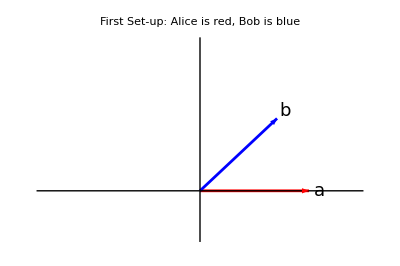

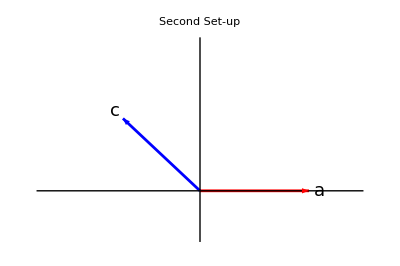

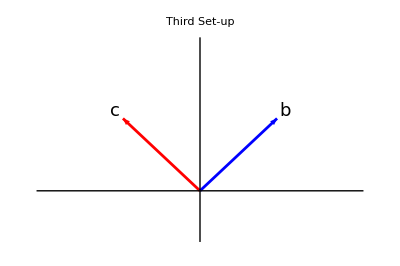

```mathematica
Show[{Graphics[{Red,Thickness[0.005],Arrow[{{0,0},{1,0}}]}],
Graphics[{Blue,Thickness[0.005],Arrow[{{0,0},{Cos[π/4],Sin[π/4]}}]}],
Graphics[Line[{{-1.5,0},{1.5,0}}]],
Graphics[Line[{{0,-0.5},{0,1.5}}]],
Graphics[Text[Style["a", FontSize->18],{1.1,0}]],
Graphics[Text[Style["b", FontSize->18],{1.1Cos[π/4],1.1Sin[π/4]}]]},PlotLabel->Style["First Set-up: Alice is red, Bob is blue", FontFamily->"Helvetica", FontSize->14]
]
Show[{Graphics[{Red,Thickness[0.005],Arrow[{{0,0},{1,0}}]}],
Graphics[{Blue,Thickness[0.005],Arrow[{{0,0},{Cos[3π/4],Sin[3π/4]}}]}],
Graphics[Line[{{-1.5,0},{1.5,0}}]],
Graphics[Line[{{0,-0.5},{0,1.5}}]],
Graphics[Text[Style["a", FontSize->18],{1.1,0}]],
Graphics[Text[Style["c", FontSize->18],{1.1Cos[3π/4],1.1Sin[3π/4]}]]},
PlotLabel->Style["Second Set-up", FontFamily->"Helvetica", FontSize->14]
]
Show[{Graphics[{Red,Thickness[0.005],Arrow[{{0,0},{Cos[3π/4],Sin[3π/4]}}]}],
Graphics[{Blue,Thickness[0.005],Arrow[{{0,0},{Cos[π/4],Sin[π/4]}}]}],
Graphics[Line[{{-1.5,0},{1.5,0}}]],
Graphics[Line[{{0,-0.5},{0,1.5}}]],
Graphics[Text[Style["c", FontSize->18],{1.1Cos[3π/4],1.1Sin[3π/4]}]],
Graphics[Text[Style["b", FontSize->18],{1.1Cos[π/4],1.1Sin[π/4]}]]},
PlotLabel->Style["Third Set-up", FontFamily->"Helvetica", FontSize->14]
]
```

We must therefore adopt more flexible definitions of the probabilities p, q and r.

```mathematica
Clear[p,q,r ]
```

```mathematica
p[aliceUP_,Ψ_]:=(Transpose[aliceUP.Ψ].aliceUP.Ψ)⟦1⟧⟦1⟧
q[aliceUP_,bobUP_,Ψ_]:=(Conjugate[Transpose[bobUP.((aliceUP.Ψ)/(√((Conjugate[Transpose[aliceUP.Ψ]].aliceUP.Ψ)⟦1⟧⟦1⟧)))]].bobUP.((aliceUP.Ψ)/(√((Conjugate[Transpose[aliceUP.Ψ]].aliceUP.Ψ)⟦1⟧⟦1⟧))))⟦1⟧⟦1⟧
r[aliceDN_,bobUP_,Ψ_]:=(Conjugate[Transpose[bobUP.((aliceDN.Ψ)/(√((Conjugate[Transpose[aliceDN.Ψ]].aliceDN.Ψ)⟦1⟧⟦1⟧)))]].bobUP.((aliceDN.Ψ)/(√((Conjugate[Transpose[aliceDN.Ψ]].aliceDN.Ψ)⟦1⟧⟦1⟧))))⟦1⟧⟦1⟧
```

Bell requires that in every case the input state be the singlet state

```mathematica
Subscript[Ψ, singlet]
```

{{0},{1/(√2)},{-1/(√2)},{0}}

which is more familiar to us as Bell4.

First Bell set-up: Alice has A-meter, Bob has B-meter.

```mathematica
Subscript[p, ab]=p[𝔸up,Subscript[Ψ, singlet]]//N
Subscript[q, ab]=q[𝔸up,𝔹up,Subscript[Ψ, singlet]]//N
Subscript[r, ab]=r[𝔸dn,𝔹up,Subscript[Ψ, singlet]]//N
```

0.5

0.146447

0.853553

Second Bell set-up: Alice has A-meter, Bob has C-meter.

```mathematica
Subscript[p, ac]=p[𝔸up,Subscript[Ψ, singlet]]
Subscript[q, ac]=q[𝔸up,ℂ𝔹up,Subscript[Ψ, singlet]]//N
Subscript[r, ac]=r[𝔸dn,ℂ𝔹up,Subscript[Ψ, singlet]]//N
```

1/2

0.853553

0.146447

Third Bell set-up: Alice has C-meter, Bob has B-meter.

```mathematica
Subscript[p, cb]=p[ℂ𝔸up,Subscript[Ψ, singlet]]//N
Subscript[q, cb]=q[ℂ𝔸up,𝔹up,Subscript[Ψ, singlet]]//N
Subscript[r, cb]=r[ℂ𝔸dn,𝔹up,Subscript[Ψ, singlet]]//N
```

0.25

0.5+0. ⅈ

0.5+0. ⅈ

Mathematica complains later about those  0.ⅈ terms, which I therefore abandon:

```mathematica
Subscript[q, cb]=0.5
Subscript[r, cb]=0.5
```

0.5

0.5

We adjust the definition of  BohmProtocol  so that it can accept such information:

```mathematica
BellProtocol[x_,y_,z_,p_,q_,r_]:=Which[0⩽x<p,Which[0⩽y<q,upup,q⩽y⩽1,updn],p⩽x⩽1,Which[0⩽z<r,dnup,r⩽z⩽1,dndn]]
```

```mathematica
DataFromAB=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, ab],Subscript[q, ab],Subscript[r, ab]],{n,1,100}];
Count[DataFromAB,upup]
Count[DataFromAB,updn]
Count[DataFromAB,dnup]
Count[DataFromAB,dndn]

DataFromAC=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, ac],Subscript[q, ac],Subscript[r, ac]],{n,1,100}];
Count[DataFromAC,upup]
Count[DataFromAC,updn]
Count[DataFromAC,dnup]
Count[DataFromAC,dndn]

DataFromCB=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, cb],Subscript[q, cb],Subscript[r, cb]],{n,1,100}];
Count[DataFromCB,upup]
Count[DataFromCB,updn]
Count[DataFromCB,dnup]
Count[DataFromCB,dndn]
```

10

40

41

9

40

6

2

52

11

15

38

36

Bell asks us in each case to construct the averaged product of Alice/Bob's meter readings:

```mathematica
Subscript[P, ab]=1/100(Count[DataFromAB,upup]+Count[DataFromAB,dndn]-Count[DataFromAB,updn]-Count[DataFromAB,dnup])
Subscript[P, ac]=1/100(Count[DataFromAC,upup]+Count[DataFromAC,dndn]-Count[DataFromAC,updn]-Count[DataFromAC,dnup])
Subscript[P, cb]=1/100(Count[DataFromCB,upup]+Count[DataFromCB,dndn]-Count[DataFromCB,updn]-Count[DataFromCB,dnup])
```

-31/50

21/25

-3/50

Bell—as stated previously—argues that if quantum events were accounted for by hidden variables then we would expect those averaged products to conform to the Bell inequality Abs[P_ab-P_ac]-P_cb≤1, but in fact the inequality is violated

```mathematica
Abs[Subscript[P, ab]-Subscript[P, ac]]-Subscript[P, cb]≤1
```

False

and the violation appears—on the basis of this specific data set—to be major. For the meters Alice and Bob have been using we expected on theoretical grounds to have

```mathematica
Bell[π/4,3π/4]//N
```

1.41421

and have, by quantum experiment, obtained

```mathematica
Abs[Subscript[P, ab]-Subscript[P, ac]]-Subscript[P, cb]//N
```

1.52

This, however, is an "experimental" result, and the question arises: is the violation of Bell's inequality statistically significant? One way to settle the issue is to return to the lab, run a longer series of measurements. Those we now perform with a single keystroke:

```mathematica
DataFromAB=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, ab],Subscript[q, ab],Subscript[r, ab]],{n,1,1000}];
Count[DataFromAB,upup]
Count[DataFromAB,updn]
Count[DataFromAB,dnup]
Count[DataFromAB,dndn]

DataFromAC=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, ac],Subscript[q, ac],Subscript[r, ac]],{n,1,1000}];
Count[DataFromAC,upup]
Count[DataFromAC,updn]
Count[DataFromAC,dnup]
Count[DataFromAC,dndn]

DataFromCB=Table[BellProtocol[Random[],Random[],Random[],Subscript[p, cb],Subscript[q, cb],Subscript[r, cb]],{n,1,1000}];
Count[DataFromCB,upup]
Count[DataFromCB,updn]
Count[DataFromCB,dnup]
Count[DataFromCB,dndn]
Subscript[P, ab]=1/1000(Count[DataFromAB,upup]+Count[DataFromAB,dndn]-Count[DataFromAB,updn]-Count[DataFromAB,dnup])//N
Subscript[P, ac]=1/1000(Count[DataFromAC,upup]+Count[DataFromAC,dndn]-Count[DataFromAC,updn]-Count[DataFromAC,dnup])//N
Subscript[P, cb]=1/1000(Count[DataFromCB,upup]+Count[DataFromCB,dndn]-Count[DataFromCB,updn]-Count[DataFromCB,dnup])//N
Abs[Subscript[P, ab]-Subscript[P, ac]]-Subscript[P, cb]//N
```

75

425

431

69

440

53

71

436

133

122

369

376

-0.712

0.752

0.018

1.446

The final figure has again to be compared with

```mathematica
√2//N
```

1.41421

and is, in any event, convincingly greater than 1.000.

This experiment was first performed in a real live laboratory by Alain Aspect (1982).

```mathematica
Hyperlink["Experimental Violation of Bell's Inequality","http://en.wikipedia.org/wiki/Alain_Aspect"]
```

Happily, Bell—though he died young—did live long enough to learn of Aspect's accomplishment.

```mathematica
Hyperlink["John Bell","http://en.wikipedia.org/wiki/John_Stewart_Bell"]
```

Bell's "no-go demonstration" has been (very productively) criticised by people on the ground that it provides only statistical evidence that hidden variable theories of the sort contemplated by Bell cannot account for the essential elements of quantum statistics. But in that respect it is precisely responsive to von Neumann, for that is the point von Neumann's "proof" was devised to establish.